# Plotting terminal branch length distribution

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/ncov-wh/branch-length-distribution

## Terminal branch lengths

```mathematica
tips=Import["terminal_branches.tsv"];
```

```mathematica
tips=Map[{#[[1]],29904*#[[2]]}&,tips];
```

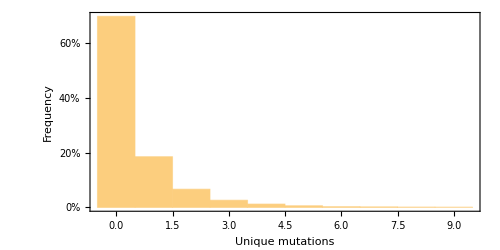

```mathematica
Histogram[tips[[All,2]],{-0.5,10,1},"Probability",PlotRange->{0,All},AspectRatio->0.5,ImageSize->500,PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"Unique mutations","Frequency"},FrameTicks->{{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.1}],Automatic},{Automatic,Automatic}}]
```

```mathematica
Length[tips]
```

111697

```mathematica
Count[tips,x_/;x[[2]]≥5]
```

860

```mathematica
N[Count[tips,x_/;x[[2]]≥5]/Length[tips]]
```

0.0076994

## Metadata

```mathematica
metadata=Import["../data/metadata.tsv"];
```

```mathematica
header=metadata[[1]]
```

{strain,virus,gisaid_epi_isl,genbank_accession,date,region,country,division,location,region_exposure,country_exposure,division_exposure,segment,length,host,age,sex,Nextstrain_clade,pangolin_lineage,GISAID_clade,originating_lab,submitting_lab,authors,url,title,paper_url,date_submitted}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{strain→1,virus→2,gisaid_epi_isl→3,genbank_accession→4,date→5,region→6,country→7,division→8,location→9,region_exposure→10,country_exposure→11,division_exposure→12,segment→13,length→14,host→15,age→16,sex→17,Nextstrain_clade→18,pangolin_lineage→19,GISAID_clade→20,originating_lab→21,submitting_lab→22,authors→23,url→24,title→25,paper_url→26,date_submitted→27}

```mathematica
metadata=Drop[metadata,1];
```

```mathematica
gisaidToDate=Map[#[[3]]->ToString[#[[5]]]&,metadata];
```

```mathematica
gisaidToCountry=Map[#[[3]]->ToString[#[[7]]]&,metadata];
```

## Recent subset from USA

```mathematica
dispatchDate=Dispatch[gisaidToDate];
```

```mathematica
dispatchCountry=Dispatch[gisaidToCountry];
```

```mathematica
USASubset=Cases[tips,x_/;(x[[1]]/.dispatchCountry)=="USA"];
```

```mathematica
Length[USASubset]
```

26524

```mathematica
recentUSASubset=Cases[USASubset,x_/;AlphabeticOrder["2020-08-01",(x[[1]]/.dispatchDate)]==1];
```

```mathematica
Length[recentUSASubset]
```

2112

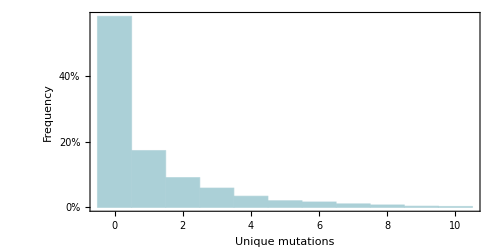

```mathematica
fig=Histogram[recentUSASubset[[All,2]],{-0.5,11,1},"Probability",PlotRange->{0,All},AspectRatio->0.5,ImageSize->500,PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"Unique mutations","Frequency"},FrameTicks->{{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.1}],Automatic},{Automatic,Automatic}},ChartStyle->Lighter[ColorData["Rainbow"][0.35],0.5]]
```

```mathematica
Export["unique_mutations.png",fig,"PNG",ImageResolution->300]
```

unique_mutations.png

```mathematica
Length[recentUSASubset]
```

2112

```mathematica
Count[recentUSASubset,x_/;x[[2]]≥5]
```

102

```mathematica
N[Count[recentUSASubset,x_/;x[[2]]≥5]/Length[recentUSASubset]]
```

0.0482955